```mathematica
ode=y'[x]-√(1-y[x]^2)==0
```

-√(1-y[x]^2)+y'[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,y[x],x]]
```

{{y[x]→Sin[x+C[1]]}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,y[0]==0},y[x],x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→Sin[x]}}

```mathematica
ya[x_]:=y[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ya[x],x]]
```

Cos[x]

```mathematica
dyadx[x_]:=Cos[x]
```

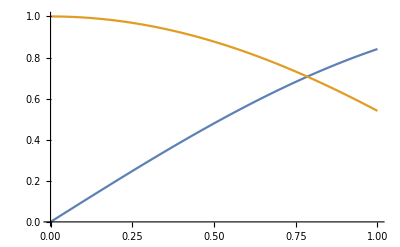

```mathematica
Plot[{ya[x],dyadx[x]},{x,0,1}]
```

```mathematica
Limit[y/(√(1-y^2)),y->1]
```

(-ⅈ) ∞